# Numerical ODE Solvers: Explicit RK Schemes

## Standard Reductions

Black box ODE solvers usually solve 1st order systems.  We are going to define a generic Runge-Kutta scheme from the Butcher Tableau. From simplicity we focus on the autonomous n-dimensional IVP 
	y'=f(y)  and y(0)=y_0
defined by the function f:ℝ^n→ℝ^n and the initial condition y_0.

## Explicit Runge Kutta (RK) Schemes Butcher Tableau

Explicit RK methods are specified by a Butcher Tableau 
	c | A
  | b	
The strictly lower triangular matrix A tells you how to compute a sequence of internal slopes. The row vector b tells you how to combine the internal slopes at the end. The column vector c (which can be computed from A) tells you each fractional sub-step.

For the first step of our IVP 
	y'=f(y) and y(0)=y_0	
the sequence of internal slopes (called K_1,K_2,…) defined by the
	K_1 | = | f(y_0)
K_2 | = | f(y_0+A_21 K_1)
K_3 | = | f(y_0+A_31 K_1+A_32 K_2)
K_4 | = | f(y_0+A_41 K_1+A_42 K_2+A_43 K_3)
⋮ | ⋮ | ⋮
while our actual step is 
	y_1 | = | y_0+h (b_1 K_1+b_2 K_2+…)
Each internal slopes is called a stage. The work intensity of an RK scheme is evaluated by the number of function evaluations required for a step.

```mathematica
RK[f_,{A_List,b_List}][{h_,t_,y_}]:=Module[{k=Length[A],Ks},
(* Compute Internal Slopes *)
Ks[1]=f[y];
Do[
Ks[i]=f[y+h*Sum[A⟦i,j⟧ Ks[j],{j,1,i-1}]],
{i,1,k}];
(* Compute and Return Output *)
{h,t+h,y+h*Sum[b⟦i⟧ Ks[i],{i,1,k}]}
]
```

Lets see if this matches the specific code from before for the Ralston RK Scheme

```mathematica
RalstonStep[f_][{h_,t_,y_}]:= Module[{K1,K2},
K1=f[y];
K2 = f[y+2h/3 K1];
{h,t+h,y+h(1/4* K1 +3/4* K2)}]
RalstonTableau={({{0, 0}, {2/3, 0}}),{1/4,3/4}};
f[y_]:= y
{t,y}={0.0,1.0};
h=0.1;
RalstonStep[f][{h,t,y}]
RK[f,RalstonTableau][{h,t,y}]
```

{0.1,0.1,1.105}

{0.1,0.1,1.105}

Lets define a fancier RK scheme from the Wiki page

```mathematica
RKSimpsonTableau={({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, 1, 0}}),{1/6,1/3,1/3,1/6}};
```

Lets see if we can solve our boring test problem y'=y that we know the answer to.

```mathematica
f[y_]:= y
{t,y}={0.0,1.0};
h=0.01; MaxIter=100;
yData=Table[{t,E^t},{t,0,1,h}];
RalstonData=NestList[RK[f,RalstonTableau],{h,t,y},MaxIter]⟦All,{2,3}⟧;
RalstonErrorData=(yData-RalstonData)⟦All,2⟧;
SimpsonData=NestList[RK[f,RKSimpsonTableau],{h,t,y},MaxIter]⟦All,{2,3}⟧;
SimpsonErrorData=(yData-SimpsonData)⟦All,2⟧;
TabView[{
"Eyeball Norm"->Show[
Plot[E^t,{t,0,1},PlotStyle->Green],
ListPlot[{RalstonData,SimpsonData},
PlotLegends->{"R","S"}],
AxesLabel->{"t","y"}
],
"Error"->ListLogPlot[
Abs[{RalstonErrorData,SimpsonErrorData}],
GridLines->Automatic,
PlotLegends->{"R","S"},
Frame->True,
FrameLabel->{"step","||err||"}]
}]
```

12

We should check the order of these two schemes using the stuff from before.

## Embedded Tableaux

A Butcher Tableau 
	c | A
  | b
b̂	
with two row vectors b and b̂ describes two different RK methods which use the same internal slopes.  The methods are compared to automatically adjust the step size h.  There is a partial list of embedded RK methods on Wikipedia at
	 https://en.wikipedia.org/wiki/List_of_Runge%E2%80%93Kutta_methods#Embedded_methods.
Our target is to implement an embedded explicit RK method from such a Butcher Table and understand the  error estimation process. The first thing to do is code and get a feel for this “better and OK” approximation process.

```mathematica
BogakiShampineTableau={
({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 3/4, 0, 0}, {2/9, 1/3, 4/9, 0}}),
{2/9,1/3,4/9,0},
{7/24,1/4,1/3,1/8}};
RK2B[f_,{A_List,b_List,bStar_List}][{h_,t_,y_}]:=Module[{k=Length[A],Ks},
(* Compute Internal Slopes *)
Ks[1]=f[y];
Do[
Ks[i]=f[y+h*Sum[A⟦i,j⟧ Ks[j],{j,1,i-1}]],
{i,1,k}];
(* Returning the better and OK approximations *)
{y+h*Sum[b⟦i⟧ Ks[i],{i,1,k}],y+h*Sum[bStar⟦i⟧ Ks[i],{i,1,k}]}
]
```

Checking using the “most-boring” example. The first one has the smaller error

```mathematica
Clear[f,y]
f[y_]:=y
{t0,y0}={0.0,1.0};
h=0.2;
RK2B[f,BogakiShampineTableau][{h,t0,y0}]
RK2B[f,BogakiShampineTableau][{h,t0,y0}]-E^h
```

Lets make a picture and see how things behave with h. Remember all we really care about is the order. In other words we only care about the power of h!

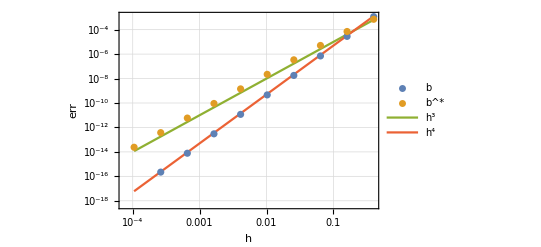

```mathematica
hList=Table[0.4^i,{i,1,10}];
{bErrs,bStarErrs}=Table[ Abs[RK2B[f,BogakiShampineTableau][{h,t0,y0}]-E^h],{h,hList}]ᵀ;ListLogLogPlot[{{hList,bErrs}ᵀ,{hList,bStarErrs}ᵀ,{hList,0.01 hList^3}ᵀ,{hList,0.05 hList^4}ᵀ},
Joined->{False,False,True,True},
GridLines->Automatic,Frame->True,FrameLabel->{"h","err"},
PlotLegends->{"b","b^*","h^3","h^4"},PlotRange->All]
```

This is another way to check for typos.  We can see that the better “b” scheme has order 3 since its single step error matches C h^(3+1). We can see that the OK "b^*" scheme has order 2 since its single step error matches Ĉ h^(2+1).

Error Control

In general the two different methods described by b and b̂ have orders p and p-1 respectively.  The different orders are used to estimate how big an step h would have been consistent with a specified error tolerance for a single step.  The key is that we have
	y(t+h)-y_1=O(h^(p+1))≈C h^(p+1) and y(t+h)-(ŷ)_1=O(h^(p-1+1))≈Ĉ h^p.
We can use the difference between y_1 and (ŷ)_1 to estimate the error as follows
	||y_1-(ŷ)_1||=||(y_1-y(t+h))-((ŷ)_1-y(t+h))||≤ C h^(p+1)+Ĉ h^p≈Ĉ h^p
In words, the difference between the two estimates is an error estimate for the lower order (ŷ)_1 scheme if the higher order y_1 scheme is working properly.  In essence, we assume that the higher order scheme is sufficiently accurate that we can use it to estimate the error in the lower order scheme!

### Is a step OK?

Since we know y_1 and (ŷ)_1 and h and p we can compute
	Ĉ=||y_1-(ŷ)_1||/h^p
so that
	||y_1-(ŷ)_1||=Ĉ h^p.
We can check that our error estimates satisfy an absolute tolerance condition
	||y_1-(ŷ)_1||≤Tol_abs
and/or a relative tolerance condition
	(||y_1-(ŷ)_1||)/(||y_1||)≤Tol_rel.
What should we do if the step fails one (or both) of these tests?  Simple, reduce the value of h and retry the step.

### Could we have taken a bigger step?

We have an estimate for how big an error we made
	||y_1-(ŷ)_1||=Ĉ h^p
If Ĉ h^p≤Tol_abs then we think we could have taken a bigger step
	h_abs=γ h
where Ĉ γ^p h^p=γ^p||y_1-(ŷ)_1||=Tol_abs so
	γ_abs=(Tol_abs/||y_1-(ŷ)_1||)^(1/p)≥1.
If (||y_1-(ŷ)_1||)/(||y_1||)≤Tol_rel then we think we could have taken a bigger step
	h_rel=γ h
where (Ĉ γ^p h^p)/(||y_1||)=γ^p(||y_1-(ŷ)_1||)/(||y_1||)=Tol_rel so
	γ_rel=((||y_1|| Tol_rel)/(||y_1-(ŷ)_1||))^(1/p)≥1.

### Automatic Step Size Control?

The automatic step size control just puts these ideas together with some “safety” factors to avoid tiny steps (basically a minimum step size that throws a warning and stops the solver) and a fudge factor (usually 0.9) which backs of the maximum step estimate.   Here is a possible implementation with only a relative error tolerance.

```mathematica
RKAdaptive[f_,{ExtendedTableau_,p_},RelTol_][{h_,t_,y_}]:=Module[
{yBetter,yStar,AbsErr,NormBetter,RelErr,γRel,CHat},
{yBetter,yStar}=RK2B[f,ExtendedTableau][{h,t,y}];
AbsErr=Norm[yBetter-yStar];
NormBetter=Norm[yBetter];
RelErr= AbsErr/NormBetter;
Print[{RelErr, RelTol}];
γRel=0.9((NormBetter*RelTol)/AbsErr)^(1/p);
Print[γRel];
If[RelErr<RelTol, 
{γRel h, t+h,yBetter},
{0.5 h, t,y}]
]
```

This definitely needs to be tested!

```mathematica
Clear[f,y,p,RelTol]
p=4;
RelTol=10.0^-3;
f[y_]:=y
{h,t,y}={0.1,0.0,1.0}

NestList[
RKAdaptive[f,{BogakiShampineTableau,p},RelTol],{h,t,y},6]
```

{0.1,0.,1.}

{0.0000207359,0.001}

2.37171

{0.000271281,0.001}

1.24706

{0.000519749,0.001}

1.05997

{0.000616459,0.001}

1.0157

{0.000645206,0.001}

1.00419

{0.000653152,0.001}

1.00113

{{0.1,0.,1.},{0.237171,0.1,1.10517},{0.295767,0.337171,1.40082},{0.313504,0.632938,1.88245},{0.318427,0.946442,2.57478},{0.319763,1.26487,3.53905},{0.320123,1.58463,4.87092}}